```mathematica
(*Para ejecutar este programa se tienen que ejecutar los programas: Golden section search y Kramers-Kronig_Dielectric_function*)
```

## Constantes

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
omega=Range[0,10,0.01];
```

```mathematica
h c/5
```

248.14

## Funciones generales

```mathematica
(*Función que devuelve la parte real y la imaginaria de la función dieléctrica a partir del índice de refracción*)
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[eps_,intervalos_]:=GoldenSearchMax[eps,##]&@@@intervalos;
(*Lorentziana*)
lorentz[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 5 lorentzianas*)
lorentzSum[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentz[ω,ω01,γ1]+A2 lorentz[ω,ω02,γ2]+A3 lorentz[ω,ω03,γ3]+A4 lorentz[ω,ω04,γ4]+A5 lorentz[ω,ω05,γ5];

(*Definición de 3 lorentzianas*)
lorentzSum4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:=A1 lorentz[ω,ω01,γ1]+A2 lorentz[ω,ω02,γ2]+A3 lorentz[ω,ω03,γ3]+A4 lorentz[ω,ω04,γ4];
```

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280]
parteRe28=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]];
(*Se definen la parte real e imaginaria de la función dieléctrica*)
parteRe287[x_]:=parteRe[x,28.7]
```

InterpolatingFunction[…]

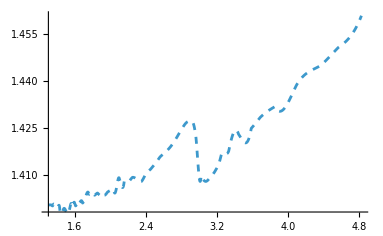

```mathematica
Plot[{Style[parteRe28[x],Dashed],parteRe287[x]},{x,1.3,4.83},PlotRange->All]
```

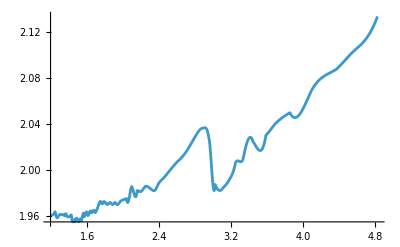

```mathematica
Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

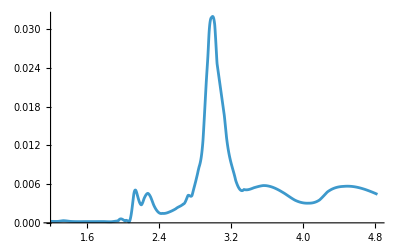

```mathematica
Plot[{epsIm[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
eps28[x_]:=epsIm[parteRe28,parteIm28,x];
ω0i28=ω0i[eps28,intervalos28];
```

```mathematica
ω0i28
```

{2.13396,2.27349,2.99459,3.56451,4.49601}

InterpolatingFunction::dmval: Input value {4.83329} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84329} lies outside the range of data in the interpolating function. Extrapolation will be used.

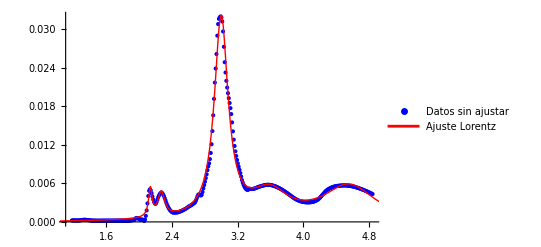

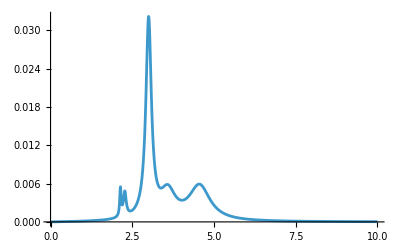

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};
(*Datos para ajuste*)
eps28Data=Table[{x,eps28[x]},{x,xmin,xmax,0.01}];
(* Ajustar con NonlinearModelFit*)
fit28=NonlinearModelFit[eps28Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28[ω],{ω,0,10},PlotRange->All]
```

```mathematica
fit28["BestFitParameters"]
```

{A1→0.000478218,ω01→2.13791,γ1→0.0515111,A2→0.000879683,ω02→2.27217,γ2→0.101576,A3→0.0188735,ω03→3.00207,γ3→0.20242,A4→0.00837223,ω04→3.59768,γ4→0.554354,A5→0.0194709,ω05→4.57488,γ5→0.779377}

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.13915×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

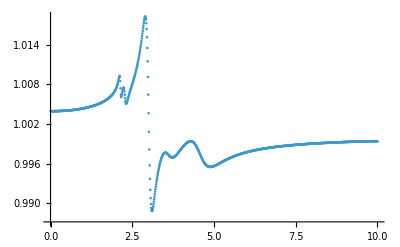

General::stop: Further output of StyleBox[RowBox[{\"Set\", \"::\", \"setraw\"}], \"MessageName\"] will be suppressed during this calculation.

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm028=Table[fit28[x],{x,0,10,0.01}];
parteReKK128=kkrebook[omega,parteIm028];
ListPlot[Transpose[{omega,parteReKK128}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,«29»,1.004,1.004,1.00401,1.00401,1.00401,1.00402,1.00402,1.00403,1.00403,1.00403,«951»}.

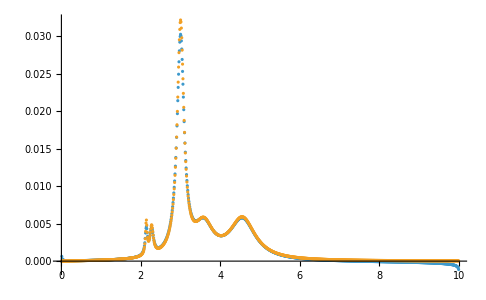

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK128=kkimbook[omega,parteReKK128];
ListPlot[{Transpose[{omega,parteImKK128}],Transpose[{omega,parteIm028}]},PlotRange->All]
```

```mathematica
eps28KK=selfconsbook[omega,parteReKK128,parteIm028,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,1.00394,«29»,1.004,1.004,1.00401,1.00401,1.00401,1.00402,1.00402,1.00403,1.00403,1.00403,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

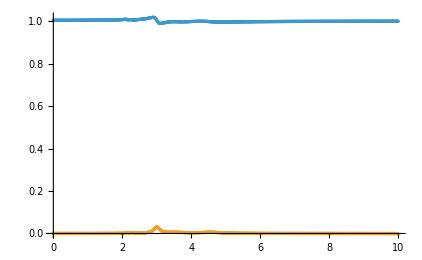

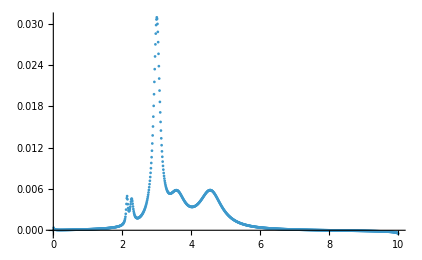

```mathematica
ListPlot[{Transpose[{omega,eps28KK[[1]]}],Transpose[{omega,eps28KK[[2]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps28KK[[2]]}]},PlotRange->All]
```

## Concentración 15.3 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuA=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\15.3_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA=Drop[datosuA,1];
datos1uA=Map[ToExpression,datos1uA,{2}];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)

datos2im=h c/datos1uA[[All,1]];
(*Obtener la parte imaginaria del índice de refracción a partir del coeficiente de absorción*)
datos3im=((datos1uA[[All,2]]*10^(-6))/(4*Pi))*datos1uA[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm15=Interpolation[Transpose[{datos2im,datos3im}],InterpolationOrder->1];
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]];
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];
(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1)
parteRe15[x_]:=parteRe[x,15.3]
```

Drop::drop: Cannot drop positions 1 through 1 in datosBeta.

Drop::drop: Cannot drop positions 1 through 1 in datosH2O.

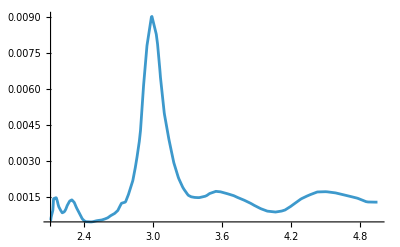

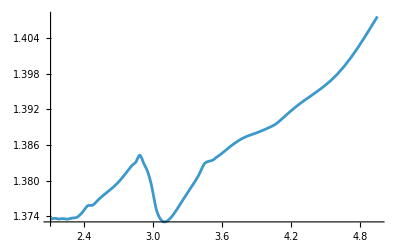

```mathematica
Plot[parteIm15[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe15[x],{x,2.11,4.95},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos15={{2.13,2.15},{2.2,2.3},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps15[x_]:=epsIm[parteRe15,parteIm15,x];
ω0i15=ω0i[eps15,intervalos15];
```

{A1→0.00038588,ω01→2.15578,γ1→0.0540998,A2→0.000696207,ω02→2.29124,γ2→0.0998999,A3→0.0150846,ω03→3.00069,γ3→0.207769,A4→0.00608215,ω04→3.60191,γ4→0.509673,A5→0.0182383,ω05→4.61002,γ5→0.875224}

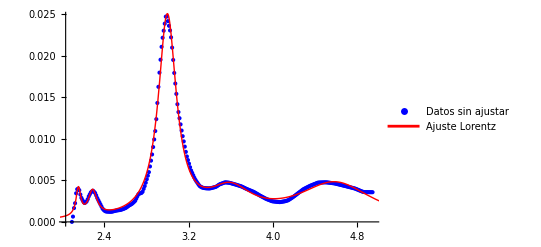

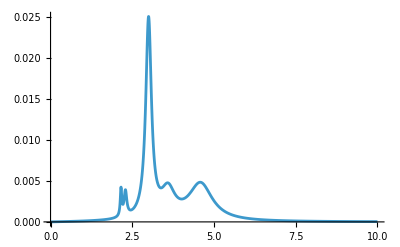

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin15,xmax15}={Min[datos2im],Max[datos2im]};
(*Datos para ajuste*)
eps15Data=Table[{x,eps15[x]},{x,xmin15,xmax15,0.01}];
(* Ajustar con NonlinearModelFit*)
fit15=NonlinearModelFit[eps15Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i15[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i15[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i15[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i15[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i15[[5]]},{γ5,0.1}},ω];
fit15["BestFitParameters"]
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit15[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit15[ω],{ω,0,10},PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 9.59078×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

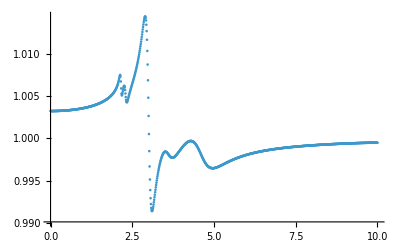

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm015=Table[fit15[x],{x,0,10,0.01}];
parteReKK115=kkrebook[omega,parteIm015];
ListPlot[Transpose[{omega,parteReKK115}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,«29»,1.00326,1.00326,1.00327,1.00327,1.00327,1.00327,1.00328,1.00328,1.00328,1.00329,«951»}.

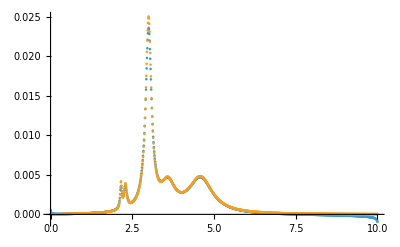

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK115=kkimbook[omega,parteReKK115];
ListPlot[{Transpose[{omega,parteImKK115}],Transpose[{omega,parteIm015}]},PlotRange->All]
```

```mathematica
eps15KK=selfconsbook[omega,parteReKK115,parteIm015,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,1.00321,«29»,1.00326,1.00326,1.00327,1.00327,1.00327,1.00327,1.00328,1.00328,1.00328,1.00329,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

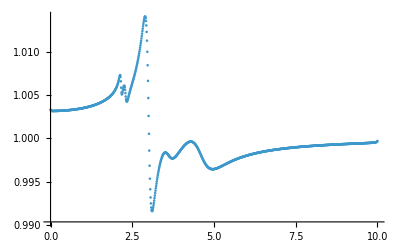

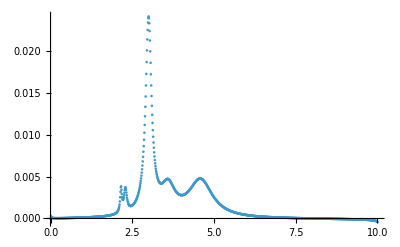

```mathematica
ListPlot[{Transpose[{omega,eps15KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps15KK[[2]]}]},PlotRange->All]
```

## Concentración 30.6 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
```

```mathematica
datosuA30=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],InterpolationOrder->1];
parteRe30[x_]:=parteRe[x,30.6]
```

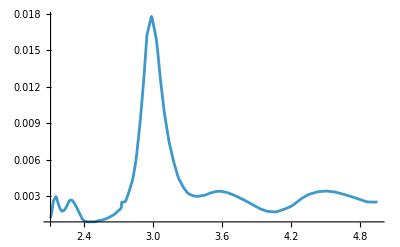

```mathematica
Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
```

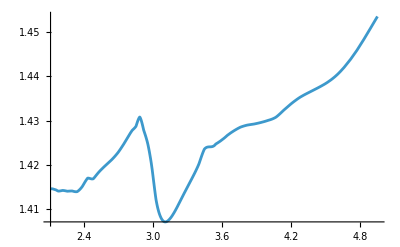

```mathematica
Plot[parteRe30[x],{x,2.11,4.95}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos30={{2,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps30[x_]:=epsIm[parteRe30,parteIm30,x];
ω0i30=ω0i[eps30,intervalos30];
```

InterpolatingFunction::dmval: Input value {2.0382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.0618} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.07639} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

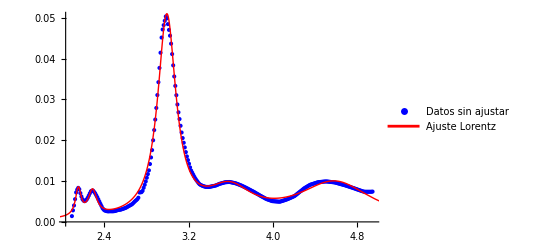

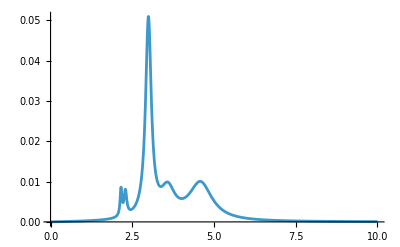

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};
(*Datos para ajuste*)
eps30Data=Table[{x,eps30[x]},{x,xmin30,xmax30,0.01}];
(* Ajustar con NonlinearModelFit*)
fit30=NonlinearModelFit[eps30Data,lorentzSum[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i30[[1]]},{γ1,0.01},{A2,0.01},{ω02,ω0i30[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0i30[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i30[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i30[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps30Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit30[ω],{ω,0,10},PlotRange->All]
```

```mathematica
fit30["BestFitParameters"]
```

{A1→0.000934244,ω01→2.15536,γ1→0.0649986,A2→0.00140568,ω02→2.29042,γ2→0.100008,A3→0.0309532,ω03→2.99583,γ3→0.210141,A4→0.013214,ω04→3.59489,γ4→0.529275,A5→0.0370468,ω05→4.60695,γ5→0.858215}

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 2.01135×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

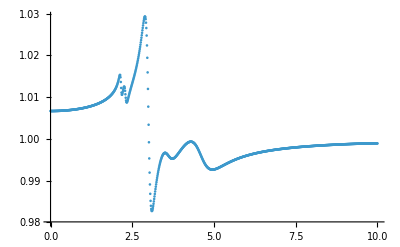

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm030=Table[fit30[x],{x,0,10,0.01}];
parteReKK130=kkrebook[omega,parteIm030];
ListPlot[Transpose[{omega,parteReKK130}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.00667,1.00667,1.00667,1.00667,1.00667,1.00667,1.00667,1.00668,1.00668,1.00668,1.00668,«29»,1.00678,1.00678,1.00679,1.00679,1.0068,1.0068,1.00681,1.00682,1.00682,1.00683,«951»}.

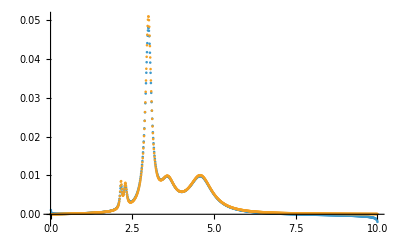

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK130=kkimbook[omega,parteReKK130];
ListPlot[{Transpose[{omega,parteImKK130}],Transpose[{omega,parteIm030}]},PlotRange->All]
```

```mathematica
eps30KK=selfconsbook[omega,parteReKK130,parteIm030,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.00667,1.00667,1.00667,1.00667,1.00667,1.00667,1.00667,1.00668,1.00668,1.00668,1.00668,«29»,1.00678,1.00678,1.00679,1.00679,1.0068,1.0068,1.00681,1.00682,1.00682,1.00683,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

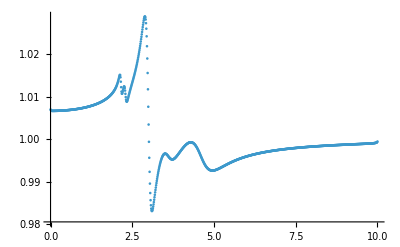

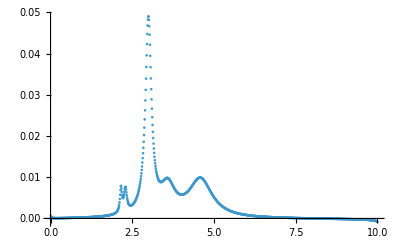

```mathematica
ListPlot[{Transpose[{omega,eps30KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps30KK[[2]]}]},PlotRange->All]
```

## Comparación entre concentraciones

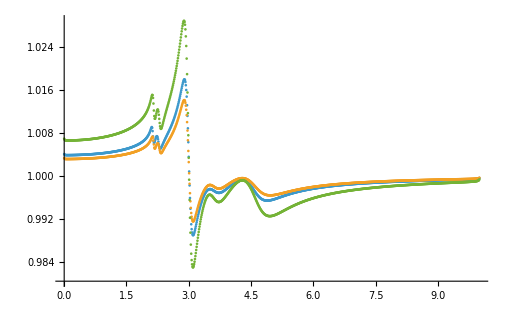

```mathematica
ListPlot[{Transpose[{omega,eps28KK[[1]]}],Transpose[{omega,eps15KK[[1]]}],Transpose[{omega,eps30KK[[1]]}]},PlotRange->All]
```

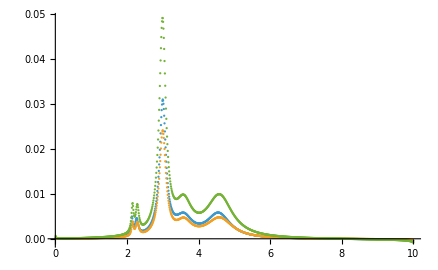

```mathematica
ListPlot[{Transpose[{omega,eps28KK[[2]]}],Transpose[{omega,eps15KK[[2]]}],Transpose[{omega,eps30KK[[2]]}]},PlotRange->All]
```

## Plasma

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuAPlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\uA_ImN_Plasma.csv"];
datosRePlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\ReN_Plasma.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uAPlasma=Drop[datosuAPlasma,1];
datos1RePlasma=Drop[datosRePlasma,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2imPlasma=h c/datos1uAPlasma[[All,1]];
datos2rePlasma=h c/datos1RePlasma[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3imPlasma=datos1uAPlasma[[All,2]]*10^(-6)*datos1uAPlasma[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteImPlasma=Interpolation[Transpose[{datos2imPlasma,datos3imPlasma}],InterpolationOrder->1];
parteRePlasma=Interpolation[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]]
```

InterpolatingFunction[…]

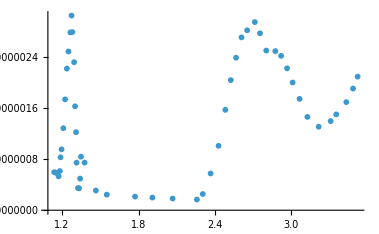

```mathematica
ListPlot[Transpose[{datos2imPlasma,datos3imPlasma}]]
```

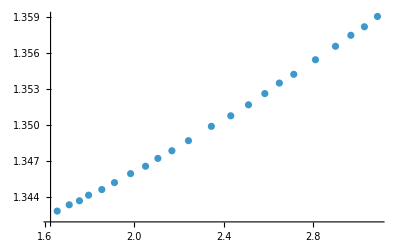

```mathematica
ListPlot[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalosPlasma={{1.2,1.3},{2.57,2.8},{2.8,2.9},{3.4,3.5}};
epsPlasma[x_]:=epsIm[parteRePlasma,parteImPlasma,x];
ω0iPlasma=ω0i[epsPlasma,intervalosPlasma];
```

InterpolatingFunction::dmval: Input value {1.2382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.2618} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.27639} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.13801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.14801} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.15801} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

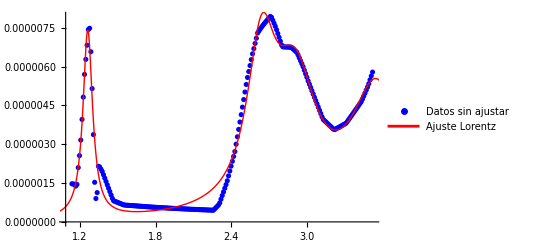

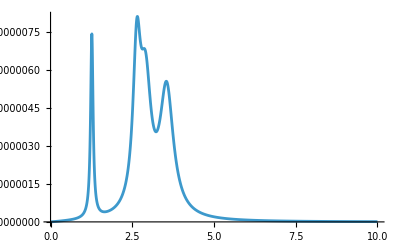

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xminPlasma,xmaxPlasma}={Min[datos2imPlasma],Max[datos2imPlasma]};
(*Datos para ajuste*)
epsPlasmaData=Table[{x,epsPlasma[x]},{x,xminPlasma,xmaxPlasma,0.01}];
(* Ajustar con NonlinearModelFit*)
fitPlasma=NonlinearModelFit[epsPlasmaData,lorentzSum4[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4],{{A1,0.01},{ω01,ω0iPlasma[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0iPlasma[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0iPlasma[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0iPlasma[[4]]},{γ4,0.05}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[epsPlasmaData,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fitPlasma[ω],{ω,xminPlasma-0.5,xmaxPlasma+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fitPlasma[ω],{ω,0,10},PlotRange->All]
```

```mathematica
fitPlasma["BestFitParameters"]
```

{A1→8.44081×10^-7,ω01→1.26439,γ1→0.09209,A2→4.32525×10^-6,ω02→2.64287,γ2→0.278515,A3→5.76062×10^-6,ω03→2.91276,γ3→0.410956,A4→8.81302×10^-6,ω04→3.55995,γ4→0.499522}

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.1541×10^-9.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

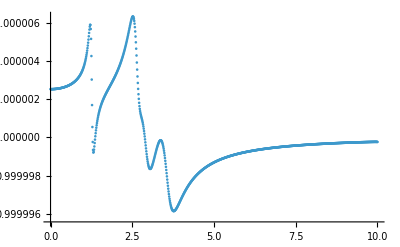

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm0Plasma=Table[fitPlasma[x],{x,0,10,0.01}];
parteReKK1Plasma=kkrebook[omega,parteIm0Plasma];
ListPlot[Transpose[{omega,parteReKK1Plasma}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«29»,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«951»}.

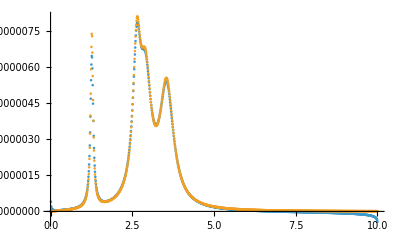

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK1Plasma=kkimbook[omega,parteReKK1Plasma];
ListPlot[{Transpose[{omega,parteImKK1Plasma}],Transpose[{omega,parteIm0Plasma}]},PlotRange->All]
```

```mathematica
epsPlasmaKK=selfconsbook[omega,parteReKK1Plasma,parteIm0Plasma,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«29»,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

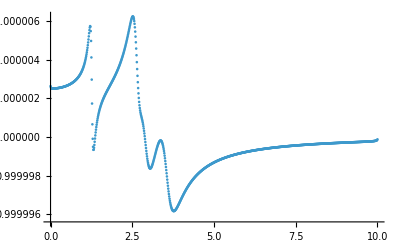

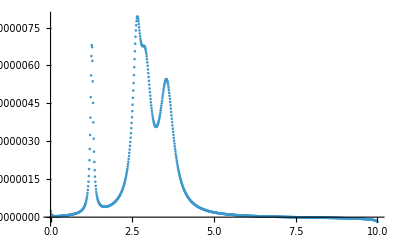

```mathematica
ListPlot[{Transpose[{omega,epsPlasmaKK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,epsPlasmaKK[[2]]}]},PlotRange->All]
```